```mathematica
(* Compute line between the points {x1,y1} and {x2,y2} *)
line[{x1_,y1_},{x2_,y2_}]:=If[x1 -x2!=0, (y2-y1)/(x2-x1)*x-y+(y2- (y2-y1)/(x2-x1)*x2),x-x1];


(* See if line l supports the polygon with vertices a1,a2,a3,a4 returns True or False *)
supp[l_, a1_,a2_,a3_,a4_]:=
Module[{vals},vals=Block[{x,y},
{l/. {x->a1[[1]],y->a1[[2]]},
l/. {x->a2[[1]],y->a2[[2]]},
l/. {x->a3[[1]],y->a3[[2]]},
l/. {x->a4[[1]],y->a4[[2]]}}];
Simplify[(And@@Thread[vals>=0])||(And@@Thread[vals<=0])]
]

(* Given outer vertex q and inner vertices p1,p2,p3,p4, find the two lines q-pi and q-pj such that the lines q-pi and q-pj support the polygon with the inner vertices, returns list with the lines that are supporting the inner polygon *)
findSupportingLines[q_,a1_,a2_,a3_,a4_]:=Module[{l1,l2,l3,l4,supportingLines},
l1=line[q,a1];
l2=line[q,a2];
l3=line[q,a3];
l4=line[q,a4];
supportingLines={};
If[l1 =!= Nothing &&supp[l1,a1,a2,a3,a4],AppendTo[supportingLines,l1]];
If[l2 =!= Nothing &&supp[l2,a1,a2,a3,a4],AppendTo[supportingLines,l2]];
If[l3 =!= Nothing &&supp[l3,a1,a2,a3,a4],AppendTo[supportingLines,l3]];
If[l4 =!= Nothing &&supp[l4,a1,a2,a3,a4],AppendTo[supportingLines,l4]];
Return[supportingLines];
];

(* Find the intersection of line l with boundary defined by s1,s2,s3,s4. Returns the intersection point v={x,y} that is not the point q *)
findIntersectionWithBoundary[l_,s1_,s2_,s3_,s4_,ineqsQ_,q_]:=Module[{linesToCheck,solsubs,v}, 
linesToCheck={s1,s2,s3,s4};
For[i=1,i<=Length[linesToCheck],i++, solsubs= Solve[l==0 && linesToCheck[[i]]==0 &&ineqsQ, {x,y},Reals]; If[solsubs =!= {}, 
v = {x,y}/.solsubs[[1]]; 
If[v[[1]]!= q[[1]] ||v[[2]]!=q[[2]], Return[v]]
];
];
Nothing
];

(* Check if inner polygon is contained in triangle. INPUT: the edges of triangle and inner vertices. Checks if edges of triangle support inner polygon. Returns True or False *)
isContained[l1v1_,l1v2_ ,lv1v2_,a1_,a2_,a3_,a4_]:=
Module[{res},res=supp[l1v1,a1,a2,a3,a4]&&supp[l1v2,a1,a2,a3,a4]&&supp[lv1v2,a1,a2,a3,a4];
If[res == True,Print["True: This is a triangle nested in between P and Q."],Print["False: This triangle is not nested between P and Q"]];
Return[res] 
]


(*Intersection point of the lines l1 and l2*)
point[l1_,l2_]:=Module[{sol},
sol = Solve[l1==0&&l2==0,{x,y}, Reals];
If[sol=!= {},{x,y}/.sol[[1]], Nothing]
]

(*Function to safely extract a point from Solve results, with check that solution is not empty *)
getPointFromSolve[eqs_,vars_]:=Module[{sol},
sol=Solve[eqs,vars,Reals];
If[sol=!={},vars/. First[sol],Nothing ]
];

(* Find the two intersection points of the line l with the boundaries s1,s2,s3,s4, satisfying the inequalities defined by ineqsQ. Returns list of intersection points vi = {xi,yi} *)
findIntersectionWithBoundaryTwoPoints[l_,s1,s2,s3,s4,ineqsQ]:= Module[{linesToCheck,intersections, v,vsubs,res},
linesToCheck={s1,s2,s3,s4};
intersections={};
For[i=1,i<=Length[linesToCheck],i++,
v=point[l,linesToCheck[[i]]];
vsubs= {x->v[[1]],y->v[[2]]};
res = Reduce[ineqsQ/.vsubs];
If[res==True, AppendTo[intersections, v]]
];
Return[intersections]
];

(* Given vertex v, find out whether the line v--innerv1 or v--innerv2 supports the polygon with vertices a1,a2,a3,a4. Returns the line l that supports the polygon. *)
findSupportingVertex[v_,innerv1_,innerv2_ ,a1_,a2_,a3_,a4_]:=Module[{innervertices,l},
innervertices = {innerv1,innerv2};
For[i=1,i<=Length[innervertices],i++,
l = line[v,innervertices[[i]]];
If [supp[l,a1,a2,a3,a4] == True, Return[l]]
]
];
```

```mathematica
Mm= {{x,y,m31,0},{5,1,5,9},{1,7,9,3},{9,7,1,3}}//Transpose;
(*Mm= {{x,y,2,0},{5,1,5,9},{1,7,9,3},{9,7,1,3}}//Transpose;*)
Mm//MatrixForm//Simplify
ysol = Solve[Det[Mm]==0,y]//Simplify
Mm=Mm/.ysol[[1]];

Mm//Simplify//MatrixForm
```

(x | 5 | 1 | 9
y | 1 | 7 | 7
m31 | 5 | 9 | 1
0 | 9 | 3 | 3)

{{y→m31+x}}

(x | 5 | 1 | 9
m31+x | 1 | 7 | 7
m31 | 5 | 9 | 1
0 | 9 | 3 | 3)

```mathematica
Mm[[2,1]]==(-m41* Det[Mm[[{1,2,3},{2,3,4}]]]+x* Det[Mm[[{2,3,4},{2,3,4}]]]+m31* Det[Mm[[{1,2,4},{2,3,4}]]])/( Det[Mm[[{1,3,4},{2,3,4}]]])/.{m41->0}//Simplify
```

True

```mathematica
MatrixRank[ Mm[[All,2;;]]]
A =   Mm[[All,2;;]]

B= {{b11,b12,b13},{1,0,0},{0,1,0},{0,0,1}}//Transpose
bsol = Solve[Mm[[{3,4},1]]== (A.B)[[{3,4},1]],{b11,b12,b13} ]//Simplify
B = B /.bsol[[1]]//Simplify;
A//MatrixForm
B//MatrixForm
```

3

{{5,1,9},{1,7,7},{5,9,1},{9,3,3}}

{{b11,1,0,0},{b12,0,1,0},{b13,0,0,1}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b12→1/8 (-2 b11+m31),b13→1/8 (-22 b11-m31)}}

(5 | 1 | 9
1 | 7 | 7
5 | 9 | 1
9 | 3 | 3)

(b11 | 1 | 0 | 0
1/8 (-2 b11+m31) | 0 | 1 | 0
1/8 (-22 b11-m31) | 0 | 0 | 1)

```mathematica
Reduce[A.B >=0,b11]
```

m31≥0&&b11≤-m31/20

```mathematica
(* Check form of first column of B*)
B[[2,1]]==(b11*Det[Mm[[{3,4},{2,4}]]]-Det[Mm[[{3,4},{1,4}]]])/-Det[Mm[[{3,4},{3,4}]]]//Simplify
B[[3,1]]==(b11*Det[Mm[[{3,4},{2,3}]]]-Det[Mm[[{3,4},{1,3}]]])/Det[Mm[[{3,4},{3,4}]]]//Simplify

(* Check that B is such that all observed entries are properly defined *)
(A.B)[[All,2;;]]==Mm[[All,2;;]]//Simplify
(A.B)[[{3,4},1]]==Mm[[{3,4},1]]//Simplify

Print["M is the same as AB when you substitute x to be the (11) entry of AB: ",  Mm==A.B/.{x->(A.B)[[1,1]]}//Simplify]
```

True

True

True

«1 more identical outputs»

M is the same as AB when you substitute x to be the (11) entry of AB: True

```mathematica
Mm = A.B//Simplify;
```

```mathematica
(*Set col sums to 1*)
colsums = Total/@Transpose[Mm];
Sm = DiagonalMatrix[colsums]//Simplify;

Om={{colsums[[2]],0,0},{colsums[[3]],1,0},{colsums[[4]],0,1}}//Simplify;

Atildepol =  A. Transpose[Inverse[Om]]//Simplify;
Atildepol//MatrixForm

Btildepol = Transpose[Om].B.Transpose[Inverse[Sm]]//Simplify;
Btildepol//Simplify//MatrixForm
(* Check that factorization was defined correctly *)
Mm .Inverse[Sm]== Atildepol.Btildepol//Simplify
```

(1/4 | -4 | 4
1/20 | 6 | 6
1/4 | 4 | -4
9/20 | -6 | -6)

(1 | 1 | 1 | 1
-(-2 b11+m31)/(320 b11) | 0 | 1/20 | 0
(22 b11+m31)/(320 b11) | 0 | 0 | 1/20)

True

```mathematica
ineqsQ=And@@Thread[(#.({1,x,y})>=0)&/@Atildepol]//Simplify
verticesP = Btildepol[[{2,3},All]]//Simplify;

(* Vertices of the inner polygon *)
p1 = verticesP[[All,1]]//Simplify
p2 = verticesP[[All,2]]
p3= verticesP[[All,3]]
p4 = verticesP[[All,4]]

(* Boundaries of Q*)
s1 = -y+1/16+x;
s2 = -x+1/16+y;
s3 = 1/120+x+y;
s4 = x+y-3/40;

(* Compute vertices of outer polygon Q *)
q1 = {x,y}/.Solve[y==1/16+x&&x+y==3/40, {x,y}][[1]];

q2 = {x,y}/.Solve[x+y==3/40&&x==1/16+y, {x,y}][[1]];
q3 = {x,y}/.Solve[x==1/16+y&&-1/120==x+y, {x,y}][[1]];
q4 = {x,y}/.Solve[y==1/16+x&&-1/120==x+y, {x,y}][[1]];
```

y≤1/16+x&&x≤1/16+y&&-1/120≤x+y≤3/40

{-(-2 b11+m31)/(320 b11),(22 b11+m31)/(320 b11)}

{0,0}

{1/20,0}

{0,1/20}

```mathematica
sol1=Solve[p1[[1]]==x,b11];
-y+p1[[2]]/.sol1[[1]]//Simplify

line[q1,q2]

Solve[p1=={1/160,11/160}, m31]
```

3/40-x-y

3/40-x-y

{{m31→0}}

```mathematica
lp1=line[q1,q2];
```

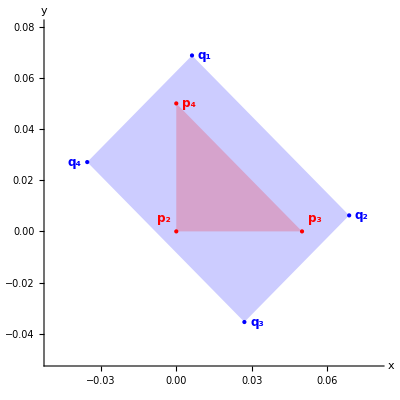

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],
(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+If[i==1,{-0.005,0.005},If[i==2,{0.005,0.005},{0.005,0}]] ],{i,Length[pVertices]}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```

### p1 is a vertex of triangle

```mathematica
(* Vertex q2 *)
p1 = q2;
q2supportingLines =  findSupportingLines[q2,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[q2supportingLines[[2]],s1,s2,s3,s4,ineqsQ,q2];

v2 = findIntersectionWithBoundary[q2supportingLines[[3]],s1,s2,s3,s4,ineqsQ,q2];



l1v1= line[p1,v1];
l1v2=line[p1,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

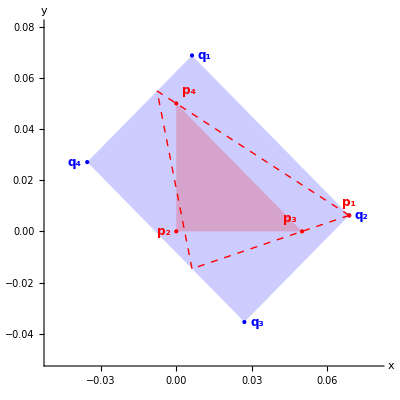

```mathematica
(*Vertices of outer polygon Q*)qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+Switch[i,1,{-0.005,0},2,{-0.005,0.005},3,{0.005,0.005},_,{0.005,0}]],{i,Length[pVertices]}],

Red,PointSize[Large],Point[p1],Text[Style[Subscript["p",1],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p1+{0,0.005}],

(*Draw dashed lines for the given equations*)
Dashed,Line[{p1, v1}],
Line[{p1,v2}],
Line[{v1, v2 }]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```

#### First critical configuration

```mathematica
p1=point[line[q3,p3],lp1];
supportingLines =  findSupportingLines[p1, p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,q2];

v2 = findIntersectionWithBoundary[supportingLines[[3]],s1,s2,s3,s4,ineqsQ,q2];



l1v1= line[p1,v1];
l1v2=line[p1,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

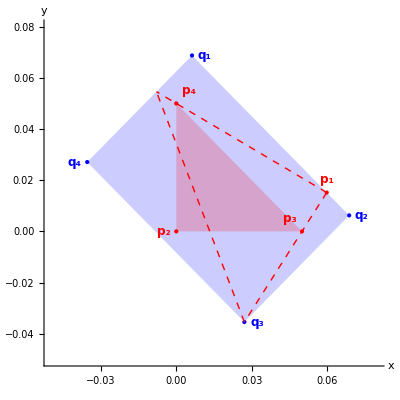

```mathematica
(*Vertices of outer polygon Q*)qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+Switch[i,1,{-0.005,0},2,{-0.005,0.005},3,{0.005,0.005},_,{0.005,0}]],{i,Length[pVertices]}],

Red,PointSize[Large],Point[p1],Text[Style[Subscript["p",1],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p1+{0,0.005}],

(*Draw dashed lines for the given equations*)
Dashed,Line[{p1, v1}],
Line[{p1,v2}],
Line[{v1, v2 }]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```

#### Second critical configuration

```mathematica
p1=point[line[q4,p4],lp1];
supportingLines =  findSupportingLines[p1,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[1]],s1,s2,s3,s4,ineqsQ,p1];

v2 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,p1];



l1v1= line[p1,v1];
l1v2=line[p1,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2,p1,p2,p3,p4]
```

{17/1120,67/1120}

{67/780-(67 x)/39-y,1/20+(11 x)/17-y}

False: This triangle is not nested between P and Q

False

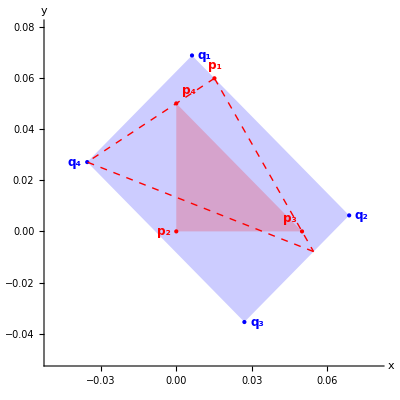

```mathematica
(*Vertices of outer polygon Q*)qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+Switch[i,1,{-0.005,0},2,{-0.005,0.005},3,{0.005,0.005},_,{0.005,0}]],{i,Length[pVertices]}],

Red,PointSize[Large],Point[p1],Text[Style[Subscript["p",1],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p1+{0,0.005}],

(*Draw dashed lines for the given equations*)
Dashed,Line[{p1, v1}],
Line[{p1,v2}],
Line[{v1, v2 }]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```

#### Third critical configuration

```mathematica
p1=point[line[q1,p3],lp1];
supportingLines =  findSupportingLines[p1,p1,p2,p3,p4];

v1 = findIntersectionWithBoundary[supportingLines[[1]],s1,s2,s3,s4,ineqsQ,p1];

v2 = findIntersectionWithBoundary[supportingLines[[2]],s1,s2,s3,s4,ineqsQ,p1];



l1v1= line[p1,v1];
l1v2=line[p1,v2];
lv1v2 = line[v1,v2];

isContained[l1v1,l1v2,lv1v2, p1,p2,p3,p4]
```

False: This triangle is not nested between P and Q

False

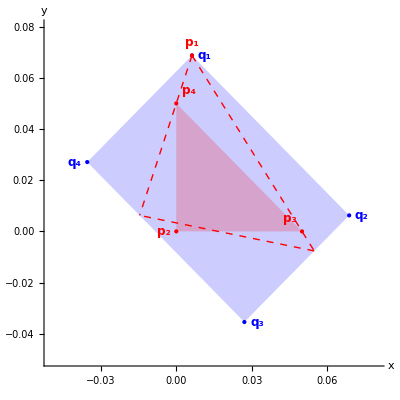

```mathematica
(*Vertices of outer polygon Q*)qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+Switch[i,1,{-0.005,0},2,{-0.005,0.005},3,{0.005,0.005},_,{0.005,0}]],{i,Length[pVertices]}],

Red,PointSize[Large],Point[p1],Text[Style[Subscript["p",1],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],p1+{0,0.005}],

(*Draw dashed lines for the given equations*)
Dashed,Line[{p1, v1}],
Line[{p1,v2}],
Line[{v1, v2 }]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```

### Edge of triangle is an edge of Q.

```mathematica
(* Considering outer edge q1q2 as edge *)
lq1p4 =line[q1,p4];
lq2p3 = line[q2,p3];

v =point[lq1p4,lq2p3];
```

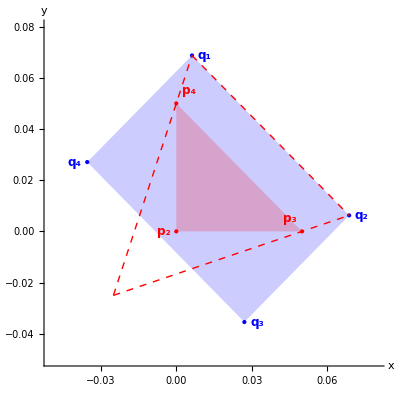

```mathematica
(*Vertices of outer polygon Q*)
qVertices={q1,q2,q3,q4};
qLabels={Subscript["q",1],Subscript["q",2],Subscript["q",3],Subscript["q",4]};

(*Vertices of the inner polygon P*)
pVertices={p2,p3,p4};
pLabels={Subscript["p",2],Subscript["p",3],Subscript["p",4]};

Show[Graphics[{
(*Draw outer polygon Q*)
Style[Polygon[qVertices],Opacity[0.2],Blue],
(*Mark the vertices of inner polygon P*)
Blue,PointSize[Large],Point[qVertices],

(*Draw inner polygon P*)
Style[Polygon[pVertices],Opacity[0.2],Red],
(*Mark the vertices of inner polygon P*)
Red,PointSize[Large],Point[pVertices],

(*Add labels to outer polygon Q vertices*)
Table[
Text[Style[qLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Blue],
qVertices[[i]]+If[i==4,{-0.005,0},{0.005,0}]],{i,Length[qVertices]}],

(*Add labels to inner polygon P vertices*)Table[Text[Style[pLabels[[i]],FontSize->12,FontFamily->"Times",FontWeight->"Bold",Red],pVertices[[i]]+Switch[i,1,{-0.005,0},2,{-0.005,0.005},3,{0.005,0.005},_,{0.005,0}]],{i,Length[pVertices]}],

(*Draw dashed lines for the given equations*)
Red,Dashed,Line[{q1,q2}],
Line[{v,q1}],
Line[{v,q2}]
}
],
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-0.05,0.08},{-0.05,0.08}},AspectRatio->1
]
```